## Initialization

### Packages, Paths, common options

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->StandardForm}];
If[FileExistsQ["~/home-uni/algebra/packages"],BaseDir="~/home-uni",BaseDir="~/uni"];
SetDirectory[BaseDir<>"/papers/sterile-nu/sim"];
$Path=Append[$Path,BaseDir<>"/algebra/packages"];
<<KPTools.m;
<<GlbPlots.m;

(* Taken from http://forums.wolfram.com/mathgroup/archive/1999/Apr/msg00028.html (slightly modified) *)
JHEPPlot[grObj_Graphics]:=Module[{fulopts,tcklst,th=0.004},
fulopts=FullOptions[grObj];
tcklst=FrameTicks/.fulopts/.{loc_,lab_,len:{_,_},{sty:___}}:>{loc,lab,2*len,{Directive[sty,Thickness[th]]}};
grObj/.Graphics[prims_,(opts__)?OptionQ]:>Graphics[prims,FrameTicks->tcklst,FrameTicksStyle->Thickness[th],FrameStyle->Thickness[th],opts]
];

KPImport[file_String,opts___]:=Module[{},
(*If[AbsoluteTime[FileDate[file]]<AbsoluteTime[{2013,3,7}],
Print[Style["Warning: File "<>file<>" is older than March 7, 2012!",FontColor->Red]];
];*)
Return[Import[file,opts]];
];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

### Reading GLoBES event rate files

```mathematica
glbSignalTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,Plus@@Data⟦1,All,All,2⟧}];
glbBGTot[Data_List]:=Transpose[{Data⟦2,1,All,1⟧,Plus@@Data⟦2,All,All,2⟧}];
glbSignalBGTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,(Plus@@Data⟦1,All,All,2⟧)+(Plus@@Data⟦2,All,All,2⟧)}];
```

## MiniBooNE

### Spectra (old version)

```mathematica
(* Read MiniBooNE data *)
DataFilesMB={"0-code/glb/mb-jk-2018/miniboone_nuedata_lowe.txt"};
DataFilesMBBG={"0-code/glb/mb-jk-2018/miniboone_nuebgr_lowe.txt"};
DataFilesMBBGStacked={"0-code/glb/mb-jk-2018/mb-all-bg-1805.12028.dat"};
DataFilesMBbar={"0-code/glb/mb-jk-2018/miniboone_nuebardata_lowe.txt"};
DataFilesMBbarBG={"0-code/glb/mb-jk-2018/miniboone_nuebarbgr_lowe.txt"};
DataFilesMBbarBGStacked={"0-code/glb/mb-jk-2018/mb-all-bg-nubarmode-1805.12028.dat"};
BinBoundaries0=Flatten[Import["0-code/glb/mb-jk-2018/miniboone_binboundaries_nue_lowe.txt","Table"]]MeV//.NN;
BinWidths0=Differences[BinBoundaries0];
BinCenters0=ListConvolve[{0.5,0.5},BinBoundaries0];
BGStyles={Null,
{Directive[Thin,Black],GrayLevel[.6]},
{Directive[Thin,Black],RGBColor[0.529,0.4,0.341]},
{Directive[Thin,Black],RGBColor[0.867,0.729,0.529]},
{Directive[Thin,Black],RGBColor[0.812,0.373,0.38]},
{Directive[Thin,Black],RGBColor[0.518,0.761,0.639]},
{Directive[Thin,Black],RGBColor[0.690,0.812,0.78]}
};
For[i=1,i≤Length[DataFilesMB],i++,
BinBoundaries[i]=BinBoundaries0;
BinWidths[i]=BinWidths0;
BinCenters[i]=BinCenters0;
DataMB[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMB⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBBG[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMBBG⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBBGStacked[i]=Cases[Import[DataFilesMBBGStacked⟦i⟧,"Table"],{Repeated[_?NumericQ]}]*MeV^-1//.NN;
MBSystUpperInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-2⟧,DataMBBGStacked[i]⟦1,-2⟧]}//.NN],InterpolationOrder->0];
MBSystLowerInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-1⟧,DataMBBGStacked[i]⟦1,-1⟧]}//.NN],InterpolationOrder->0];
MBSystCenterInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-3⟧,DataMBBGStacked[i]⟦1,-3⟧]}//.NN],InterpolationOrder->0];
PlotListObs[i]=MapThread[{{#1⟦1⟧/GeV,#1⟦2⟧/#2/MeV^-1},ErrorBar[#2/2/GeV,N[Sqrt[#⟦2⟧]]/#2/MeV^-1]}//.NN&,{DataMB[i],BinWidths[i]}];
MyPlotObs[i]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black]];
MyPlotBGStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries[i]/GeV,Append[DataMBBGStacked[i]⟦All,j⟧,DataMBBGStacked[i]⟦-1,j⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->BGStyles⟦j,1⟧,Filling->{1->{Bottom,BGStyles⟦j,2⟧}}],{j,Length[DataMBBGStacked[i]⟦1⟧]-2,2,-1}]
(*RegionPlot[MBSystLowerInterpol[x GeV]<y/MeV<MBSystUpperInterpol[x GeV]//.NN,Evaluate[{x,BinBoundaries[i]⟦1⟧/GeV,BinBoundaries[i]⟦-1⟧/GeV}//.NN],{y,0,4.5},PlotPoints->50,Mesh->150,MeshFunctions->{#1-#2&},BoundaryStyle->None,MeshStyle->Directive[GrayLevel[.6],Thickness[.002]],PlotStyle->Transparent],
ListPlot[{Transpose[{BinBoundaries[i]/GeV,Append[DataMBBGStacked[i]⟦All,-2⟧,DataMBBGStacked[i]⟦-1,-2⟧]/MeV^-1}//.NN],
Transpose[{BinBoundaries[i]/GeV,Append[DataMBBGStacked[i]⟦All,-1⟧,DataMBBGStacked[i]⟦-1,-1⟧]/MeV^-1}//.NN]},
Joined->True,InterpolationOrder->0,PlotStyle->None,Filling->{1->{{2},GrayLevel[0,.2]}}]*)];

DataMBbar[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMBbar⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBbarBG[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMBbarBG⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBbarBGStacked[i]=Cases[Import[DataFilesMBbarBGStacked⟦i⟧,"Table"],{Repeated[_?NumericQ]}]*MeV^-1//.NN;
MBbarSystUpperInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBbarBGStacked[i]⟦All,-2⟧,DataMBbarBGStacked[i]⟦1,-2⟧]}//.NN],InterpolationOrder->0];
MBbarSystLowerInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBbarBGStacked[i]⟦All,-1⟧,DataMBbarBGStacked[i]⟦1,-1⟧]}//.NN],InterpolationOrder->0];
MBbarSystCenterInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBbarBGStacked[i]⟦All,-3⟧,DataMBbarBGStacked[i]⟦1,-3⟧]}//.NN],InterpolationOrder->0];

PlotListObsBar[i]=MapThread[{{#1⟦1⟧/GeV,#1⟦2⟧/#2/MeV^-1},ErrorBar[#2/2/GeV,N[Sqrt[#⟦2⟧]]/#2/MeV^-1]}//.NN&,{DataMBbar[i],BinWidths[i]}];
MyPlotObsBar[i]=ErrorListPlot[PlotListObsBar[i],PlotRange->All,PlotStyle->Directive[Thick,Black]];
MyPlotBGbarStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries[i]/GeV,Append[DataMBbarBGStacked[i]⟦All,j⟧,DataMBbarBGStacked[i]⟦-1,j⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->BGStyles⟦j,1⟧,Filling->{1->{Bottom,BGStyles⟦j,2⟧}}],{j,Length[DataMBbarBGStacked[i]⟦1⟧]-2,2,-1}]];
];
```

```mathematica
(* make plot illustrating the systematic uncertainty on (sig+bg) - neutrino mode *)
i=1;
MyPlotSyst[i]=RegionPlot[MBSystLowerInterpol[x GeV]<y/MeV-EventsTotalInterpol[i][x GeV]+MBSystCenterInterpol[x GeV]<MBSystUpperInterpol[x GeV]//.NN,Evaluate[{x,BinBoundaries[1]⟦1⟧/GeV,BinBoundaries[1]⟦-1⟧/GeV}//.NN],{y,0,6},PlotPoints->200,Mesh->150,MeshFunctions->{#1-#2&},BoundaryStyle->None,MeshStyle->Directive[GrayLevel[.6],Thickness[.002]],PlotStyle->GrayLevel[0,.1]];
```

```mathematica
(* Read spectrum from Joachim's code *)
MyTunes={"default","gibuu","nuance","nuwro","G18_01a_02_11a","G18_01b_02_11a","G18_02a_02_11a","G18_02b_02_11a","G18_10a_02_11a","G18_10b_02_11a"};
MyTunesHumanReadable={"MB prediction","GiBUU","NUANCE","NuWro",
"GENIE G18_01a_02_11a","GENIE G18_01b_02_11a","GENIE G18_02a_02_11a","GENIE G18_02b_02_11a","GENIE G18_10a_02_11a","GENIE G18_10b_02_11a"};
MyTuneColors={RGBColor[1,.7,.7],RGBColor[.8,0,0],RGBColor[0,.8,0],RGBColor[.8,.8,0],
RGBColor[0.034,0.054,0.458],RGBColor[0.068,0.171,0.468],RGBColor[0.105,0.287,0.478],RGBColor[0.139,0.384,0.487],
RGBColor[0.175,0.471,0.497],RGBColor[0.203,0.52,0.462],RGBColor[0.229,0.552,0.395],RGBColor[0.253,0.581,0.332],RGBColor[0.306,0.613,0.279]};
MyTuneLineStyles={Dashing[{}],Dashed,DotDashed,Dotted};
DataFiles=MyTunes/.s_String:>"3-3p1/mbbg/dm41s22thmueUm4-mbjk-"<>s<>".dat";
(*DataFiles⟦1⟧="3-3p1/mbbg/dm41s22thmueUm4-mbjk-default-test.dat"; (* FIXME FIXME *)*)
MyStyles={Directive[Thick,Dashed,Black],Directive[Thick,Blue]};
For[i=1,i≤Length[DataFiles],i++,
DataRaw[i]=Import[DataFiles⟦i⟧,"Text"];
DM41[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*Best.*point.*DM41 *([-+0-9eE\\.]* ).*"]:>"$1"]];
s22thmue[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*Best.*point.*s22thmue *([-+0-9eE\\.]* ).*"]:>"$1"]];
Uμ4[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*Best.*point.*Um4 *([-+0-9eE\\.]* ).*"]:>"$1"]];

DataJK[i]=Cases[Import[DataFiles⟦i⟧],{"#","MBJKSPECT",x__}:>{x}];
EventsSignal[i]=Transpose[{BinCenters[1],DataJK[i]⟦All,1⟧}];
EventsBG[i]=Transpose[{BinCenters[1],DataJK[i]⟦All,2⟧}];
EventsTotal[i]=Transpose[{BinCenters[1],Total/@DataJK[i]⟦All,{1,2}⟧}];
(*EventsSignalBar[i]=Transpose[{BinCenters[1],DataJK[i]⟦All,3⟧}];
EventsBGbar[i]=Transpose[{BinCenters[1],DataJK[i]⟦All,4⟧}];
EventsTotalBar[i]=Transpose[{BinCenters[1],Total/@DataJK[i]⟦All,{3,4}⟧}];*)
];
```

```mathematica
(* Plot spectra *)
For[i=1,i≤Length[DataFiles],i++,
(* make signal plot - neutrino mode *)
PlotListSignal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[1],Append[EventsSignal[i],EventsSignal[i]⟦-1⟧],Append[BinWidths[1],BinWidths[1]⟦-1⟧]}];
MyPlotSignal[i]=ListPlot[PlotListSignal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[MyTuneColors⟦i⟧,Dashed]];

(* make background plot - neutrino mode *)
PlotListBG[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[1],Append[EventsBG[i],EventsBG[i]⟦-1⟧],Append[BinWidths[1],BinWidths[1]⟦-1⟧]}];
MyPlotBG[i]=ListPlot[PlotListBG[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[MyTuneColors⟦i⟧,Dotted](*Filling->{{1->{Bottom,RGBColor[.8,.6,.8]}}}*)];

(* make plot of total rate (sig+bg) - neutrino mode *)
EventsTotalInterpol[i]=Interpolation[Transpose[{BinBoundaries[1],
Prepend[EventsTotal[i]⟦All,-1⟧/BinWidths[1],EventsTotal[i]⟦1,-1⟧/BinWidths[1]⟦-1⟧]}//.NN],InterpolationOrder->0];
PlotListTotal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[1],Append[EventsTotal[i],EventsTotal[i]⟦-1⟧],Append[BinWidths[1],BinWidths[1]⟦-1⟧]}];
MyPlotTotal[i]=Show[ListPlot[PlotListTotal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦Mod[i-1,4]+1⟧]]];

(* make plot illustrating the systematic uncertainty on (sig+bg) - neutrino mode *)
(*MyPlotSyst[i]=RegionPlot[MBSystLowerInterpol[x GeV]<y/MeV-EventsTotalInterpol[i][x GeV]+MBSystCenterInterpol[x GeV]<MBSystUpperInterpol[x GeV]//.NN,Evaluate[{x,BinBoundaries[1]⟦1⟧/GeV,BinBoundaries[1]⟦-1⟧/GeV}//.NN],{y,0,6},PlotPoints->200,Mesh->150,MeshFunctions->{#1-#2&},BoundaryStyle->None,MeshStyle->Directive[GrayLevel[.6],Thickness[.002]],PlotStyle->GrayLevel[0,.1]];*)

(* make plot of total rate (sig+bg) - antineutrino mode *)
(*EventsTotalBarInterpol[i]=Interpolation[Transpose[{BinBoundaries[1],
Prepend[EventsTotalBar[i]⟦All,-1⟧/BinWidths[1],EventsTotalBar[i]⟦1,-1⟧/BinWidths[1]⟦-1⟧]}//.NN],InterpolationOrder->0];
PlotListTotalBar[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[1],Append[EventsTotalBar[i],EventsTotalBar[i]⟦-1⟧],Append[BinWidths[1],BinWidths[1]⟦-1⟧]}];
MyPlotTotalBar[i]=Show[ListPlot[PlotListTotalBar[i],InterpolationOrder->0,Joined->True,PlotStyle->MyStyle]];*)

(* make plot illustrating the systematic uncertainty on (sig+bg) - neutrino mode *)
(*MyPlotSystBar[i]=RegionPlot[MBbarSystLowerInterpol[x GeV]<y/MeV-EventsTotalBarInterpol[i][x GeV]+MBbarSystCenterInterpol[x GeV]<MBbarSystUpperInterpol[x GeV]//.NN,Evaluate[{x,BinBoundaries[1]⟦1⟧/GeV,BinBoundaries[1]⟦-1⟧/GeV}//.NN],{y,0,6},PlotPoints->200,Mesh->150,MeshFunctions->{#1-#2&},BoundaryStyle->None,MeshStyle->Directive[GrayLevel[.6],Thickness[.002]],PlotStyle->GrayLevel[0,.1]];*)
];
```

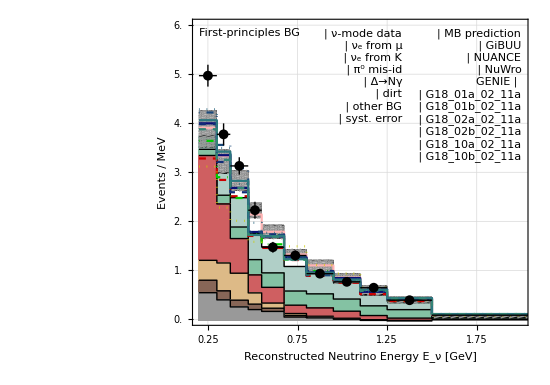
-Graphics-Brdar Kopp 2021

```mathematica
MyLegend1[1]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black]],"ν-mode data"},
{LegendBox[BGStyles⟦7,2⟧,BGStyles⟦7,1⟧],"ν_e from μ"},
{LegendBox[BGStyles⟦6,2⟧,BGStyles⟦6,1⟧],"ν_e from K"},
{LegendBox[BGStyles⟦5,2⟧,BGStyles⟦5,1⟧],"π^0 mis-id"},
{LegendBox[BGStyles⟦4,2⟧,BGStyles⟦4,1⟧],"Δ→Nγ"},
{LegendBox[BGStyles⟦3,2⟧,BGStyles⟦3,1⟧],"dirt"},
{LegendBox[BGStyles⟦2,2⟧,BGStyles⟦2,1⟧],"other BG"},
{Show[LegendBox[GrayLevel[0,.1]],RegionPlot[True,{x,0,1},{y,0,1},Mesh->6,MeshFunctions->{#1-2#2&},BoundaryStyle->None,MeshStyle->Directive[Black,Thickness[.007]],PlotStyle->Transparent]],"syst. error"}
},ItemSize->{Automatic,1.3},Spacings->{Automatic,0}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegend1[2]=Framed[Grid[{
Sequence@@Table[{LegendLine[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦Mod[i-1,4]+1⟧]],MyTunesHumanReadable⟦i⟧},
{i,1,4}],
{Style["GENIE",Bold],SpanFromLeft},
Sequence@@Table[{LegendLine[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦Mod[i-1,4]+1⟧]],StringReplace[MyTunesHumanReadable⟦i⟧,"GENIE ":>""]},
{i,5,Length[DataFiles]}]
},ItemSize->{Automatic,1.3},Spacings->{Automatic,{0,0,0,0,0.4,0,0,0,0,0,0,0}}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegend2[i]=Framed[Grid[{
{"sin^22θ_μe","=",ToString[Round[s22thmue[i],0.001]]},
{"|U_μ4|^2","=",ToString[Round[Uμ4[i]^2,0.0001]]},
{"m_4","=",ToString[Round[Sqrt[N[DM41[i]]]]]<> " eV"}
},ItemSize->{Automatic,1.3}, Spacings->{0.3,0},Alignment->{{Right,Center,Left},Baseline},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyPlot[1]=Overlay[{JHEPPlot[Show[
MyPlotBGStacked[1],MyPlotSyst[1],Sequence@@Table[MyPlotTotal[i],{i,1,Length[DataFiles]}],MyPlotObs[1],
PlotRange->{{0.2,2.},{0,6.0}},ImagePadding->{{60,20},{50,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","Events / MeV"},
Epilog->{
Inset[MyLegend1[1],Scaled[{0.625,0.97}],{1,1}],
Inset[MyLegend1[2],Scaled[{0.98,0.97}],{1,1}],
Text[Framed[If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"Data-driven BG","First-principles BG"]],Scaled[{0.02,0.97}],{-1,1},Background->GrayLevel[1,.7]]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
```

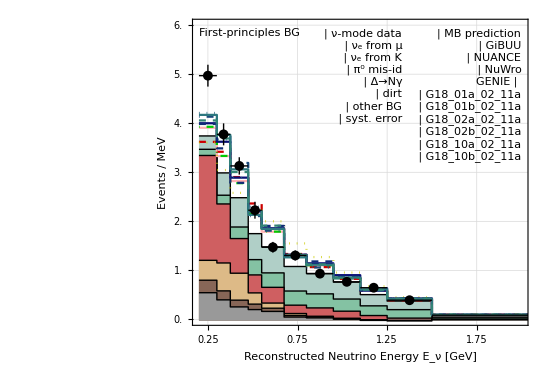
-Graphics-Brdar Kopp 2021

```mathematica
(* no modified CC BG *)
```

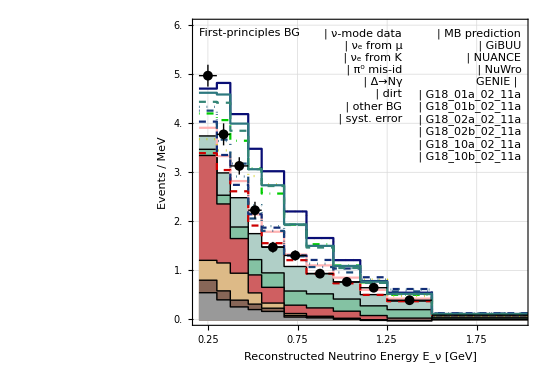
-Graphics-Brdar Kopp 2020

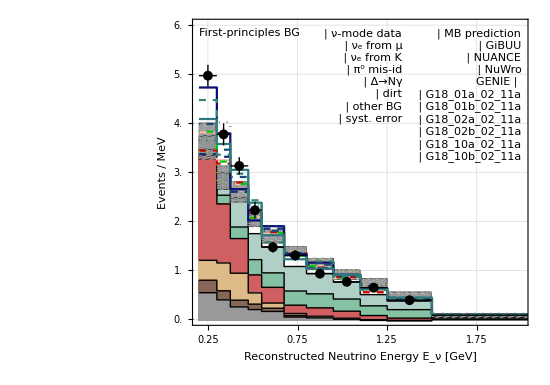
-Graphics-Brdar Kopp 2020

```mathematica
(* CC BG in both e and mu *)
```

```mathematica
Export["~/mb-spectrum-generator-comparison.pdf",MyPlot[1]]
```

~/mb-spectrum-generator-comparison.pdf

### Covariance Matrix

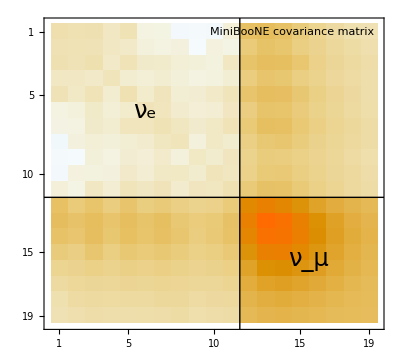

```mathematica
DataFilesCov={"default"}/.s_String:>"3-3p1/mbbg/dm41s22thmueUm4-mbjk-cov-"<>s<>".dat";
For[i=1,i≤1+0Length[DataFilesCov],i++,
DataCov[i]=Import[DataFilesCov⟦i⟧,"Table"];
McovInv[i]=Cases[DataCov[i],{"#","McovInv",x__}:>{x}];
McovInv[i]=McovInv[i]⟦1;;Length[McovInv[i]]/2⟧; (* covariance matrix appears twice in the files, cut away the 2nd occurrence *)
MyMcovPlot[i]=Overlay[{MatrixPlot[Inverse[McovInv[i]]⟦1;;19,1;;19⟧,PlotLegends->Automatic,
(*Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},*)
Epilog->{
Line[{{11,-1},{11,100}}],
Line[{{-1,19-11},{100,19-11}}],
Text[Style["ν_e",FontSize->24],{5.5,19-5.5}],
Text[Style["ν_μ",FontSize->24],{11+4,19-11-4}],
Text[Framed["MiniBooNE covariance matrix"],Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]]
}](*,Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]*)},Alignment->{0.9,1}];
];
Grid[{{MyMcovPlot[1]}}]
Export["fig/mb-cov-matrix.pdf",MyMcovPlot[1]];
```

### Spectra

```mathematica
(* Read MiniBooNE data *)
Clear[DataMB];
DataFilesMB={"0-code/glb/mb-jk-2018/miniboone_nuedata_lowe.txt"};
DataFilesMBBG={"0-code/glb/mb-jk-2018/miniboone_nuebgr_lowe.txt"};
DataFilesMBBGStacked={"0-code/glb/mb-jk-2018/mb-all-bg-1805.12028.dat"};
DataFilesMBbar={"0-code/glb/mb-jk-2018/miniboone_nuebardata_lowe.txt"};
DataFilesMBbarBG={"0-code/glb/mb-jk-2018/miniboone_nuebarbgr_lowe.txt"};
DataFilesMBbarBGStacked={"0-code/glb/mb-jk-2018/mb-all-bg-nubarmode-1805.12028.dat"};
DataFilesMBmu={"0-code/glb/mb-jk-2018/miniboone_numudata.txt"};
DataFilesMBmuPred={"0-code/glb/mb-jk-2018/miniboone_numu.txt"};
DataFilesMBmubar={"0-code/glb/mb-jk-2018/miniboone_numubardata.txt"};
DataFilesMBmubarPred={"0-code/glb/mb-jk-2018/miniboone_numubar.txt"};
BinBoundaries0=Flatten[Import["0-code/glb/mb-jk-2018/miniboone_binboundaries_nue_lowe.txt","Table"]]MeV//.NN;
BinWidths0=Differences[BinBoundaries0];
BinCenters0=ListConvolve[{0.5,0.5},BinBoundaries0];
BinBoundariesMu0=Flatten[Cases[Import["0-code/glb/mb-jk-2018/miniboone_binboundaries_numu.txt","Table"],{_?NumericQ}]]MeV//.NN;
BinWidthsMu0=Differences[BinBoundariesMu0];
BinCentersMu0=ListConvolve[{0.5,0.5},BinBoundariesMu0];
BGStyles={Null,
{Directive[Thin,Black],GrayLevel[.6]},
{Directive[Thin,Black],RGBColor[0.529,0.4,0.341]},
{Directive[Thin,Black],RGBColor[0.867,0.729,0.529]},
{Directive[Thin,Black],RGBColor[0.812,0.373,0.38]},
{Directive[Thin,Black],RGBColor[0.518,0.761,0.639]},
{Directive[Thin,Black],RGBColor[0.690,0.812,0.78]}
};
For[i=1,i≤Length[DataFilesMB],i++,
BinBoundaries[i]=BinBoundaries0;
BinWidths[i]=BinWidths0;
BinCenters[i]=BinCenters0;
DataMB[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMB⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBBGStacked[i]=Cases[Import[DataFilesMBBGStacked⟦i⟧,"Table"],{Repeated[_?NumericQ]}]*MeV^-1//.NN;
DataMBBG[i]=Differences/@(ReplacePart[#,1->0.]&/@DataMBBGStacked[i]⟦All,1;;7⟧);
MBSystUpperInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-2⟧,DataMBBGStacked[i]⟦1,-2⟧]}//.NN],InterpolationOrder->0];
MBSystLowerInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-1⟧,DataMBBGStacked[i]⟦1,-1⟧]}//.NN],InterpolationOrder->0];
MBSystCenterInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-3⟧,DataMBBGStacked[i]⟦1,-3⟧]}//.NN],InterpolationOrder->0];

BinBoundariesMu[i]=BinBoundariesMu0;
BinWidthsMu[i]=BinWidthsMu0;
BinCentersMu[i]=BinCentersMu0;
DataMBmu[i]=Transpose[{BinCentersMu0,Flatten[Cases[Import[DataFilesMBmu⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBmuPred[i]=Transpose[{BinCentersMu0,Flatten[Cases[Import[DataFilesMBmuPred⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]/BinWidthsMu0}];

PlotListObs[i]=MapThread[{{#1⟦1⟧/GeV,#1⟦2⟧/#2/MeV^-1},ErrorBar[#2/2/GeV,N[Sqrt[#⟦2⟧]]/#2/MeV^-1]}//.NN&,{DataMB[i],BinWidths[i]}];
MyPlotObs[i]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black]];
MyPlotMBBGStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries[i]/GeV,Append[DataMBBGStacked[i]⟦All,j⟧,DataMBBGStacked[i]⟦-1,j⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->BGStyles⟦j,1⟧,Filling->{1->{Bottom,BGStyles⟦j,2⟧}}],{j,Length[DataMBBGStacked[i]⟦1⟧]-2,2,-1}]];

PlotListObsMu[i]=MapThread[{{#1⟦1⟧/GeV,#1⟦2⟧/#2/MeV^-1},ErrorBar[#2/2/GeV,N[Sqrt[#⟦2⟧]]/#2/MeV^-1]}//.NN&,{DataMBmu[i],BinWidthsMu[i]}];
MyPlotObsMu[i]=ErrorListPlot[PlotListObsMu[i],PlotRange->All,PlotStyle->Directive[Thick,Black]];
MyPlotMBmuPred[i]=ListPlot[Transpose[{BinBoundariesMu[i]/GeV,Append[DataMBmuPred[i]⟦All,2⟧,DataMBmuPred[i]⟦-1,2⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->Directive[Thin,Black],Filling->{1->{Bottom,RGBColor[.8,.8,1]}}]
];
```

```mathematica
(* Read spectrum from Joachim's code *)
MyTunes={"default-nobgosc","default","default",
"gibuu","nuance","nuwro",
"G18_01a_02_11a","G18_01b_02_11a","G18_02a_02_11a","G18_02b_02_11a","G18_10a_02_11a","G18_10b_02_11a"};
MyTunesHumanReadable={"MB fit (w/o BG osc.)","MB fit (with BG osc.)","MB fit (w/ BG osc.)",
"GiBUU","NUANCE","NuWro",
"GENIE G18_01a_02_11a","GENIE G18_01b_02_11a","GENIE G18_02a_02_11a","GENIE G18_02b_02_11a","GENIE G18_10a_02_11a","GENIE G18_10b_02_11a"};
MyTuneColors={RGBColor[0,0,1],RGBColor[0,0,1],RGBColor[0,0,1],
RGBColor[0,0,.7],RGBColor[.7,0,.7],RGBColor[.7,.7,0],
RGBColor[1,0,0],RGBColor[1,0.110,0],RGBColor[1,0.220,0],RGBColor[1,0.0333,0],RGBColor[1,0.443,0],RGBColor[1,0.557,0]};
(*MyTuneColors={RGBColor[0,0,1],RGBColor[0,0,1],RGBColor[0,0,1],
RGBColor[0,0,.7],RGBColor[.7,0,.7],RGBColor[.7,.7,0],
RGBColor[0.034,0.054,0.458],RGBColor[0.068,0.171,0.468],RGBColor[0.105,0.287,0.478],RGBColor[0.139,0.384,0.487],
RGBColor[0.175,0.471,0.497],RGBColor[0.203,0.52,0.462],RGBColor[0.229,0.552,0.395],RGBColor[0.253,0.581,0.332],RGBColor[0.306,0.613,0.279]};*)
MyTuneLineStyles={Dashed,Dashing[{}],Dashing[{}],
Dashing[{}],Dashing[{}],Dashing[{}],
Dashing[{}],Dashed,DotDashed,Dotted,Dashing[{}],Dashed};
DataFiles=MyTunes/.s_String:>"3-3p1/mbbg/dm41s22thmueUm4-mbjk-"<>s<>".dat";
DataFiles=MyTunes/.s_String:>"3-3p1/mbbg/dm41s22thmueUm4-mbjk-"<>s<>"-dd.dat";
MyStyles={Directive[Thick,Dashed,Black],Directive[Thick,Blue]};
For[i=1,i≤Length[DataFiles],i++,
(* extract chi^2 values *)
DataRaw[i]=Import[DataFiles⟦i⟧,"Table"];
DataChi2[i]=Cases[DataRaw[i],{"#","CHI2",x_}:>x];
Chi2BF[i]=DataChi2[i]⟦-1⟧;
Chi2NoOsc[i]=DataChi2[i]⟦1⟧;

(* extract signal and background spectra *)
DataJK[i]=Cases[DataRaw[i],{"#","MBJKSPECT",x__}:>{x}];
DataJK[i]=Partition[DataJK[i],2*Length[BinWidths[1]]+Length[BinWidthsMu[1]]+1]; (* each block contains 11 signal entries for Subscript[ν, e], 8 entries for Subscript[ν, μ], 11 background entries, 1 params entry *)
DataJKspect[i]=DataJK[i]⟦All,1;;Length[BinWidths[1]]⟧;
DataJKbg[i]=(Cases[#,{"BG",__}]&/@DataJK[i])⟦All,All,2;;⟧;
DataJKmu[i]=(Cases[#,{"MU",__}]&/@DataJK[i])⟦All,All,2;;⟧;

(* extract parameter values *)
DataParams[i]=DataJK[i]⟦All,-1,2;;⟧;
DM41BF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"DM41",x_}:>x]⟦1⟧;
s22thmueBF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"s22thmue",x_}:>x]⟦1⟧;
Uμ4BF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"Um4",x_}:>x]⟦1⟧;
Ue4BF[i]=Cases[Partition[DataParams[i]⟦-1⟧,2],{"Ue4",x_}:>x]⟦1⟧;
];
```

```mathematica
(* Plot spectra *)
For[i=1,i≤Length[DataFiles],i++,
(* choose parameter point at which to extract rates *)

(* i=3: bfp from our full MB fit; otherwise results at individual bfp *)
(*Switch[i,
3,(jj=Flatten[Position[DataParams[i],{__,"DM41",DM41BF[2],__,"s22thmue",s22thmueBF[2],___}]];
jj=jj⟦Ordering[DataChi2[i]⟦jj⟧,1]⟧⟦1⟧); (* extract rates at bfp of "classical" MB fit *),
_,jj=Length[DataParams[i]]; (* extract rates at best fit point *)
];*)

(* extract rates at specific parameters *)
(*(jj=Flatten[Position[DataParams[i],{__,"DM41",_?(#>0.7&&#<0.9&),__,"s22thmue",_?(#<0.0002&),___}]];
jj=jj⟦Ordering[DataChi2[i]⟦jj⟧]⟦1⟧⟧); *)

(* extract rates at first point in file ≃ no oscillations *)
(*jj=1; *)

(* extract rates at best fit point *)
jj=Length[DataParams[i]];

DM41[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"DM41",x_}:>x]⟦1⟧;
s22thmue[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"s22thmue",x_}:>x]⟦1⟧;
Uμ4[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"Um4",x_}:>x]⟦1⟧;
Ue4[i]=Cases[Partition[DataParams[i]⟦jj⟧,2],{"Ue4",x_}:>x]⟦1⟧;
Chi2[i]=DataChi2[i]⟦jj⟧;

(* extract signal and background rates *)
EventsSignal[i]=Transpose[{BinCenters[1],DataJKspect[i]⟦jj,All,1⟧}];
EventsBG[i]=Transpose[{BinCenters[1],DataJKspect[i]⟦jj,All,2⟧}];
EventsBGefromμ[i]=Transpose[{BinCenters[1],DataJKbg[i]⟦jj,All,2⟧}];
EventsBGefromK[i]=Transpose[{BinCenters[1],DataJKbg[i]⟦jj,All,3⟧}];
EventsBGother[i]=Transpose[{BinCenters[1],DataJKbg[i]⟦jj,All,1⟧}];
EventsTotal[i]=Transpose[{BinCenters[1],Total/@DataJKspect[i]⟦jj,All,{1,2}⟧}];
EventsMu[i]=Transpose[{BinCentersMu[1],DataJKmu[i]⟦jj,All,1⟧}];
EventsMuBar[i]=Transpose[{BinCentersMu[1],DataJKmu[i]⟦jj,All,2⟧}];

(* create data for stacked background histogram *)
EventsBGStacked[i]=Flatten[{#⟦1⟧,Accumulate[#⟦2;;⟧]}]&/@Transpose[{
BinCenters[1],
EventsBGother[i]⟦All,2⟧*DataMBBG[1]⟦All,1⟧/(Total/@DataMBBG[1]⟦All,1;;4⟧+1*^-100), (* "other" backgrounds *)
EventsBGother[i]⟦All,2⟧*DataMBBG[1]⟦All,2⟧/(Total/@DataMBBG[1]⟦All,1;;4⟧+1*^-100), (* dirt background *)
EventsBGother[i]⟦All,2⟧*DataMBBG[1]⟦All,3⟧/(Total/@DataMBBG[1]⟦All,1;;4⟧+1*^-100), (* Δ background *)
EventsBGother[i]⟦All,2⟧*DataMBBG[1]⟦All,4⟧/(Total/@DataMBBG[1]⟦All,1;;4⟧+1*^-100), (* π^0 background *)
EventsBGefromK[i]⟦All,2⟧, (* Subscript[ν, e] from K background *)
EventsBGefromμ[i]⟦All,2⟧ (* Subscript[ν, e] from μ background *)
}];

(* make plot of total rate (sig+bg) - neutrino mode *)
EventsTotalInterpol[i]=Interpolation[Transpose[{BinBoundaries[1],
Prepend[EventsTotal[i]⟦All,-1⟧/BinWidths[1],EventsTotal[i]⟦1,-1⟧/BinWidths[1]⟦-1⟧]}//.NN],InterpolationOrder->0];
PlotListTotal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[1],Append[EventsTotal[i],EventsTotal[i]⟦-1⟧],Append[BinWidths[1],BinWidths[1]⟦-1⟧]}];
MyPlotTotal[i]=Show[ListPlot[PlotListTotal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦Mod[i-1,4]+1⟧]]];

PlotListMu[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundariesMu[1],Append[EventsMu[i],EventsMu[i]⟦-1⟧],Append[BinWidthsMu[1],BinWidthsMu[1]⟦-1⟧]}];
MyPlotMu[i]=ListPlot[PlotListMu[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦Mod[i-1,4]+1⟧]];

(* make stacked background plot *)
If[MyTunes⟦i⟧=="default-nobgosc",
MyPlotBGStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries[1]/GeV,Append[EventsBGStacked[i]⟦All,j⟧/BinWidths[1],EventsBGStacked[i]⟦-1,j⟧/BinWidths[1]⟦-1⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->Directive[Darker[BGStyles⟦j,2⟧],Thick,Dotted]],{j,Length[EventsBGStacked[i]⟦1⟧],2,-1}]],
(* Else *)
MyPlotBGStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries[1]/GeV,Append[EventsBGStacked[i]⟦All,j⟧/BinWidths[1],EventsBGStacked[i]⟦-1,j⟧/BinWidths[1]⟦-1⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->BGStyles⟦j,1⟧,Filling->{1->{Bottom,BGStyles⟦j,2⟧}}],{j,Length[EventsBGStacked[i]⟦1⟧],2,-1}]]
];
];
```

```mathematica
(* make plot illustrating the systematic uncertainty on (sig+bg) - neutrino mode *)
i=2;
MyPlotSyst[i]=RegionPlot[MBSystLowerInterpol[x GeV]<y/MeV-EventsTotalInterpol[i][x GeV]+MBSystCenterInterpol[x GeV]<MBSystUpperInterpol[x GeV]//.NN,Evaluate[{x,BinBoundaries[1]⟦1⟧/GeV,BinBoundaries[1]⟦-1⟧/GeV}//.NN],{y,0,6},PlotPoints->200,Mesh->150,MeshFunctions->{#1-#2&},BoundaryStyle->None,MeshStyle->Directive[GrayLevel[.6],Thickness[.002]],PlotStyle->GrayLevel[0,.1]];
```

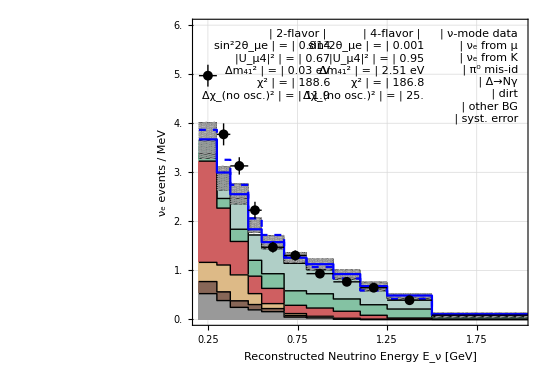
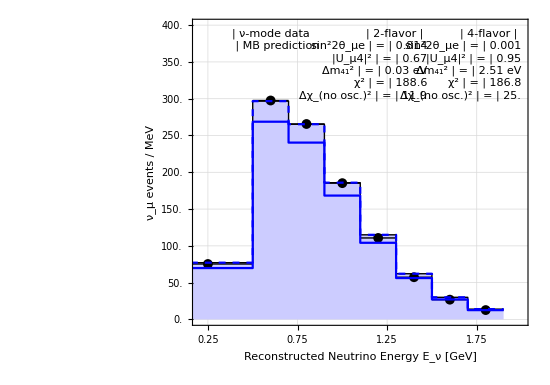
-Graphics-Brdar Kopp 2021 | -Graphics-Brdar Kopp 2021

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyLegend1[i]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black]],"ν-mode data"},
{LegendBox[BGStyles⟦7,2⟧,BGStyles⟦7,1⟧],"ν_e from μ"},
{LegendBox[BGStyles⟦6,2⟧,BGStyles⟦6,1⟧],"ν_e from K"},
{LegendBox[BGStyles⟦5,2⟧,BGStyles⟦5,1⟧],"π^0 mis-id"},
{LegendBox[BGStyles⟦4,2⟧,BGStyles⟦4,1⟧],"Δ→Nγ"},
{LegendBox[BGStyles⟦3,2⟧,BGStyles⟦3,1⟧],"dirt"},
{LegendBox[BGStyles⟦2,2⟧,BGStyles⟦2,1⟧],"other BG"},
{Show[LegendBox[GrayLevel[0,.1]],RegionPlot[True,{x,0,1},{y,0,1},Mesh->6,MeshFunctions->{#1-2#2&},BoundaryStyle->None,MeshStyle->Directive[Black,Thickness[.007]],PlotStyle->Transparent]],"syst. error"}
},ItemSize->{Automatic,1.3},Spacings->{Automatic,0}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegendMu[i]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black]],"ν-mode data"},
{LegendBox[RGBColor[.8,.8,1],Directive[Thin,Black]],"MB prediction"}
},ItemSize->{Automatic,1.3},Spacings->{Automatic,0}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegend2[i]=Framed[Grid[{
{LegendLine[Directive[MyTuneColors⟦i⟧,MyTuneLineStyles⟦Mod[i-1,4]+1⟧,Thick]],If[i==1,"2-flavor","4-flavor"],SpanFromLeft},
{"sin^22θ_μe","=",ToString[Round[s22thmue[i],0.001]]},
{"|U_μ4|^2","=",ToString[Round[Uμ4[i]^2,0.01]]},
{"Δm_41^2","=",ToString[Round[DM41[i],0.01]]<> " eV"},
{"χ^2","=",ToString[Round[Chi2[i],0.1]]},
{"Δχ_(no osc.)^2","=",ToString[Round[Chi2NoOsc[i]-Chi2[i],0.1]]}
},ItemSize->{Automatic,1.3}, Spacings->{0.3,{0,2->0.3}},Alignment->{{Right,Center,Left},Baseline,{1,1}->Center},BaseStyle->{FontSize->15},Dividers->{False,{False,2->True}}],Background->RGBColor[1,1,1,.8]];
];
i=2;
MyPlot[i]=Overlay[{JHEPPlot[Show[
MyPlotBGStacked[2],MyPlotSyst[2],MyPlotTotal[1],MyPlotTotal[2],MyPlotObs[1],
PlotRange->{{0.2,2.},{0,6.0}},ImagePadding->{{70,20},{60,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","ν_e events / MeV"},
Epilog->{
Inset[MyLegend1[i],Scaled[{0.97,0.97}],{1,1}],
Inset[MyLegend2[1],Scaled[{0.41,0.97}],{1,1}],
Inset[MyLegend2[2],Scaled[{0.69,0.97}],{1,1}]
(*Text[Framed[MyTunesHumanReadable⟦i⟧],Scaled[{0.02,0.97}],{-1,1},Background->GrayLevel[1,.7]]*)
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
MyPlot[100+i]=Overlay[{JHEPPlot[Show[
MyPlotMBmuPred[1],MyPlotObsMu[1],MyPlotMu[1],MyPlotMu[2],
PlotRange->{{0.2,2.},{0,400.}},ImagePadding->{{70,20},{60,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","ν_μ events / MeV"},
Epilog->{
Inset[MyLegendMu[1],Scaled[{0.117,0.97}],{-1,1}],
Inset[MyLegend2[1],Scaled[{0.70,0.97}],{1,1}],
Inset[MyLegend2[2],Scaled[{0.98,0.97}],{1,1}]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
Grid[{{MyPlot[2],MyPlot[102]}}]
Export["fig/mb-spectrum-nue-default.pdf",MyPlot[2]];
Export["fig/mb-spectrum-numu-default.pdf",MyPlot[102]];
```

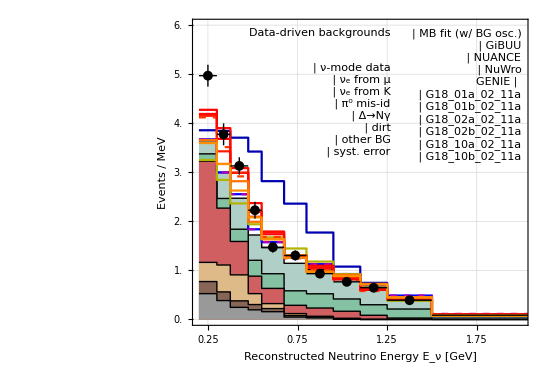
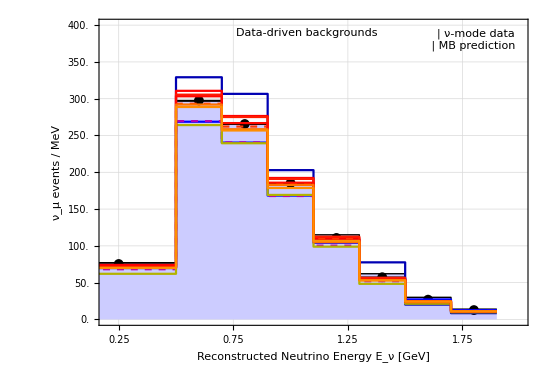
-Graphics-Brdar Kopp 2021 | -Graphics-Brdar Kopp 2021

```mathematica
MyLegend1[1]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black]],"ν-mode data"},
{LegendBox[BGStyles⟦7,2⟧,BGStyles⟦7,1⟧],"ν_e from μ"},
{LegendBox[BGStyles⟦6,2⟧,BGStyles⟦6,1⟧],"ν_e from K"},
{LegendBox[BGStyles⟦5,2⟧,BGStyles⟦5,1⟧],"π^0 mis-id"},
{LegendBox[BGStyles⟦4,2⟧,BGStyles⟦4,1⟧],"Δ→Nγ"},
{LegendBox[BGStyles⟦3,2⟧,BGStyles⟦3,1⟧],"dirt"},
{LegendBox[BGStyles⟦2,2⟧,BGStyles⟦2,1⟧],"other BG"},
{Show[LegendBox[GrayLevel[0,.1]],RegionPlot[True,{x,0,1},{y,0,1},Mesh->6,MeshFunctions->{#1-2#2&},BoundaryStyle->None,MeshStyle->Directive[Black,Thickness[.007]],PlotStyle->Transparent]],"syst. error"}
},ItemSize->{Automatic,1.3},Spacings->{Automatic,0}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegend1[2]=Framed[Grid[{
Sequence@@Table[{LegendLine[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦Mod[i-1,4]+1⟧]],MyTunesHumanReadable⟦i⟧},
{i,3,6}],
{Style["GENIE",Bold],SpanFromLeft},
Sequence@@Table[{LegendLine[Directive[Thick,MyTuneColors⟦i⟧,MyTuneLineStyles⟦Mod[i-1,4]+1⟧]],StringReplace[MyTunesHumanReadable⟦i⟧,"GENIE ":>""]},
{i,7,Length[DataFiles]}]
},ItemSize->{Automatic,1.3},Spacings->{Automatic,{0,5->0.4}}, Alignment->{Left,Baseline},Dividers->{None(*,{-4->Black}*)},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegend2[i]=Framed[Grid[{
{"sin^22θ_μe","=",ToString[Round[s22thmue[i],0.001]]},
{"|U_μ4|^2","=",ToString[Round[Uμ4[i]^2,0.0001]]},
{"m_4","=",ToString[Round[Sqrt[N[DM41[i]]]]]<> " eV"}
},ItemSize->{Automatic,1.3}, Spacings->{0.3,0},Alignment->{{Right,Center,Left},Baseline},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyPlot[1]=Overlay[{JHEPPlot[Show[
MyPlotBGStacked[2],(*MyPlotSyst[1],*)Sequence@@Table[MyPlotTotal[i],{i,3,Length[DataFiles]}],MyPlotObs[1],
PlotRange->{{0.2,2.},{0,6.0}},ImagePadding->{{70,20},{60,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","Events / MeV"},
Epilog->{
Inset[MyLegend1[1],Scaled[{0.59,0.86}],{1,1}],
Inset[MyLegend1[2],Scaled[{0.98,0.97}],{1,1}],
Text[Framed[If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"Data-driven backgrounds","First-principles backgrounds"]],Scaled[{0.59,0.97}],{1,1},Background->GrayLevel[1,.7]]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
MyPlot[101]=Overlay[{JHEPPlot[Show[
MyPlotMBmuPred[1],MyPlotObsMu[1],Sequence@@Table[MyPlotMu[i],{i,3,Length[DataFiles]}],
PlotRange->{{0.2,2.},{0,400.}},ImagePadding->{{70,20},{60,15}},GridLines->Automatic,PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","ν_μ events / MeV"},
Epilog->{
Inset[MyLegendMu[1],Scaled[{0.97,0.97}],{1,1}],
Text[Framed[If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"Data-driven backgrounds","First-principles backgrounds"]],Scaled[{0.65,0.97}],{1,1},Background->GrayLevel[1,.7]]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}];
Grid[{{MyPlot[1],MyPlot[101]}}]
OutputSuffix=If[StringCases[DataFiles⟦1⟧,RegularExpression[".*-dd\\.dat"]]≠{},"dd","fp"];
Export["fig/mb-spectrum-nue-comparison-"<>OutputSuffix<>".pdf",MyPlot[1]];
Export["fig/mb-spectrum-numu-comparison-"<>OutputSuffix<>".pdf",MyPlot[101]];
```

### Exclusion Regions in sin^2 2 θ_μe and Δm^2

```mathematica
MyTunes={"default","default-nobgosc","gibuu","nuance","nuwro","G18_01a_02_11a","G18_01b_02_11a","G18_02a_02_11a","G18_02b_02_11a","G18_10a_02_11a","G18_10b_02_11a"};
MyTunesHumanReadable={"MB prediction","MB prediction (no BG osc)","GiBUU","NUANCE","NuWro",
"GENIE G18_01a_02_11a","GENIE G18_01b_02_11a","GENIE G18_02a_02_11a","GENIE G18_02b_02_11a","GENIE G18_10a_02_11a","GENIE G18_10b_02_11a"};
DataFiles="3-3p1/mbbg/dm41s22thmueUm4-mbjk-"<>#<>".dat"&/@MyTunes;
(*DataFiles="results/dm41s22thmueUm4-mbjk-"<>#<>".dat"&/@MyTunes; (* FIXME *)*)
For[i=1,i≤Length[DataFiles],i++,
DataRaw[i]=KPImport[DataFiles⟦i⟧,"Table"];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]=Select[Data[i],#⟦3⟧<0.75&]; (* select Subscript[U, μ4] range to avoid solutions with Subscript[U, μ4]~1 *)
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,If[10^(#⟦2⟧)/(4*(10^(#⟦3⟧))^2)>0.2,1.*^12,#⟦4⟧]}&/@Data[i]; (* restrict Subscript[U, e4] range *)
Data[i]=Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
(*Data[i]=Select[#,#⟦3⟧==-1.0&]⟦1,{1,2,4}⟧&/@Data[i], (* select specific Subscript[U, μ4] *)*)
jj=Ordering[#⟦All,-1⟧,1]&/@Data[i];
DataUμ4[i]=MapThread[Flatten[{#1⟦1,1⟧,#1⟦1,2⟧,#1⟦#2,3⟧}]&,{Data[i],jj}]; (* save optimum Subscript[U, μ4] at each grid point in (s22thmue,dm41) *)
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Data[i], (* save χ^2 at optimum Subscript[U, μ4] *)

(* Else - data files in dm41, th14, th24 *)
Print["Wrong file format!"];
];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
logs22thMin[i]=Min[Data[i]⟦All,2⟧];
logs22thMax[i]=Max[Data[i]⟦All,2⟧];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
DataUμ4Interpol[i]=Interpolation[DataUμ4[i],InterpolationOrder->1];

(* Extract best fit point: Either it has been computed accurately, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"s22thmue"]],Chi2Min[i]},

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
]; (* End[if] *)

Print[DataFiles⟦i⟧];
Print["   Best fit: sin^22θ_μe=",10^BFP[i]⟦2⟧,", Δm^2=",10^BFP[i]⟦1⟧];
Chi2NoOsc[i]=DataInterpol[i][logdmsqMin[i],logs22thMin[i]];
Print["   χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
]; (* End[loop over data files] *)
```

3-3p1/mbbg/dm41s22thmueUm4-mbjk-default.dat

Best fit: sin^22θ_μe=1/100, Δm^2=0.251189

χ_min^2=192.7, χ_(no osc)^2=211.77, Δχ_(no osc.)^2=19.0691 (CL 0.999928)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-default-nobgosc.dat

Best fit: sin^22θ_μe=0.501187, Δm^2=0.0398107

χ_min^2=188.602, χ_(no osc)^2=200.489, Δχ_(no osc.)^2=11.8875 (CL 0.997378)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-gibuu.dat

Best fit: sin^22θ_μe=0.00630957, Δm^2=12.5893

χ_min^2=562.419, χ_(no osc)^2=674.668, Δχ_(no osc.)^2=112.249 (CL 1.)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-nuance.dat

Best fit: sin^22θ_μe=1/100, Δm^2=0.316228

χ_min^2=197.551, χ_(no osc)^2=216.958, Δχ_(no osc.)^2=19.4072 (CL 0.999939)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-nuwro.dat

Best fit: sin^22θ_μe=0.00251189, Δm^2=3.16228

χ_min^2=252.423, χ_(no osc)^2=272.627, Δχ_(no osc.)^2=20.2044 (CL 0.999959)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_01a_02_11a.dat

Best fit: sin^22θ_μe=0.00251189, Δm^2=7.94328

χ_min^2=191.743, χ_(no osc)^2=203.601, Δχ_(no osc.)^2=11.858 (CL 0.997339)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_01b_02_11a.dat

Best fit: sin^22θ_μe=0.00199526, Δm^2=7.94328

χ_min^2=194.469, χ_(no osc)^2=202.898, Δχ_(no osc.)^2=8.42968 (CL 0.985225)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_02a_02_11a.dat

Best fit: sin^22θ_μe=0.00251189, Δm^2=7.94328

χ_min^2=189.778, χ_(no osc)^2=199.755, Δχ_(no osc.)^2=9.97719 (CL 0.993185)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_02b_02_11a.dat

Best fit: sin^22θ_μe=0.00251189, Δm^2=7.94328

χ_min^2=190.26, χ_(no osc)^2=198.733, Δχ_(no osc.)^2=8.47327 (CL 0.985544)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_10a_02_11a.dat

Best fit: sin^22θ_μe=0.0125893, Δm^2=0.316228

χ_min^2=185.341, χ_(no osc)^2=196.677, Δχ_(no osc.)^2=11.3358 (CL 0.996545)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_10b_02_11a.dat

Best fit: sin^22θ_μe=0.00251189, Δm^2=7.94328

χ_min^2=186.8, χ_(no osc)^2=199.343, Δχ_(no osc.)^2=12.543 (CL 0.998111)

```mathematica
ss="";
For[i=1,i≤Length[DataFiles],i++,
If[i==2,Continue[]];
s="\\SI{"<>ToString[SetPrecision[10^BFP[i]⟦1⟧,2]]<>"}{eV^2}   &   "<>
ToString[SetPrecision[10^BFP[i]⟦2⟧,2]]<>"   &   "<>
ToString[SetPrecision[Select[DataUμ4[i],#⟦1⟧==BFP[i]⟦1⟧&&#⟦2⟧==BFP[i]⟦2⟧&]⟦1,3⟧^2,2]]<>"   &   "<>
ToString[SetPrecision[Chi2Min[i]/(18-2),3]]<>"   &   "<>
ToString[SetPrecision[Chi2NoOsc[i]-Chi2Min[i],3]]<>"   &   "<>
"$"<>ToString[SetPrecision[xx/.FindRoot[PValue[xx]==1-CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],{xx,2}]//Quiet,2]]<>" \\sigma$ \\\\";
ss=ss<>s<>"\n";
Print[StringCases[DataFiles⟦i⟧,RegularExpression[".*-mbjk-(.*).dat"]:>"$1"]⟦1⟧,": ",s];
];
Print[ss];
```

default: \SI{0.25}{eV^2}   &   0.01   &   0.062   &   12.0   &   19.1   &   $4.0 \sigma$ \\

gibuu: \SI{13.}{eV^2}   &   0.0063   &   0.0064   &   35.2   &   112.   &   $14. \sigma$ \\

nuance: \SI{0.32}{eV^2}   &   0.01   &   0.040   &   12.3   &   19.4   &   $4.0 \sigma$ \\

nuwro: \SI{3.2}{eV^2}   &   0.0025   &   0.026   &   15.8   &   20.2   &   $4.1 \sigma$ \\

G18_01a_02_11a: \SI{7.9}{eV^2}   &   0.0025   &   0.014   &   12.0   &   11.9   &   $3.0 \sigma$ \\

G18_01b_02_11a: \SI{7.9}{eV^2}   &   0.0020   &   0.020   &   12.2   &   8.43   &   $2.4 \sigma$ \\

G18_02a_02_11a: \SI{7.9}{eV^2}   &   0.0025   &   0.010   &   11.9   &   9.98   &   $2.7 \sigma$ \\

G18_02b_02_11a: \SI{7.9}{eV^2}   &   0.0025   &   0.0064   &   11.9   &   8.47   &   $2.4 \sigma$ \\

G18_10a_02_11a: \SI{0.32}{eV^2}   &   0.013   &   0.014   &   11.6   &   11.3   &   $2.9 \sigma$ \\

G18_10b_02_11a: \SI{7.9}{eV^2}   &   0.0025   &   0.010   &   11.7   &   12.5   &   $3.1 \sigma$ \\

\SI{0.25}{eV^2}   &   0.01   &   0.062   &   12.0   &   19.1   &   $4.0 \sigma$ \\
\SI{13.}{eV^2}   &   0.0063   &   0.0064   &   35.2   &   112.   &   $14. \sigma$ \\
\SI{0.32}{eV^2}   &   0.01   &   0.040   &   12.3   &   19.4   &   $4.0 \sigma$ \\
\SI{3.2}{eV^2}   &   0.0025   &   0.026   &   15.8   &   20.2   &   $4.1 \sigma$ \\
\SI{7.9}{eV^2}   &   0.0025   &   0.014   &   12.0   &   11.9   &   $3.0 \sigma$ \\
\SI{7.9}{eV^2}   &   0.0020   &   0.020   &   12.2   &   8.43   &   $2.4 \sigma$ \\
\SI{7.9}{eV^2}   &   0.0025   &   0.010   &   11.9   &   9.98   &   $2.7 \sigma$ \\
\SI{7.9}{eV^2}   &   0.0025   &   0.0064   &   11.9   &   8.47   &   $2.4 \sigma$ \\
\SI{0.32}{eV^2}   &   0.013   &   0.014   &   11.6   &   11.3   &   $2.9 \sigma$ \\
\SI{7.9}{eV^2}   &   0.0025   &   0.010   &   11.7   &   12.5   &   $3.1 \sigma$ \\

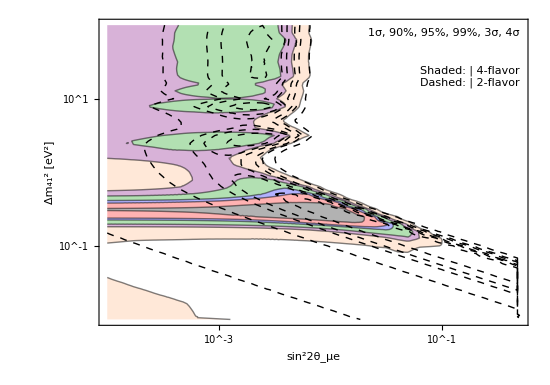
-Graphics-Brdar Kopp 2021

```mathematica
(* plots illustrating the impact of BG oscillations in MB *)
MyContours={χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyStyles={Directive[Black,Dashing[{}]],Directive[Red,Dashed],Directive[Blue,Dashing[{0.005,0.002}]],Directive[RGBColor[0,0.6,0],DotDashed],Directive[Purple,Dotted],Directive[RGBColor[1,0.7,0.5],Dashing[{}]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[1,0,0,.3],RGBColor[0,0,1,.3],RGBColor[0,0.6,0,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
For[i=1,i≤2,i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{{-4,Log10[0.5]},Full,Full},Contours->MyContours,
ContourShading->If[MyTunes⟦i⟧=="default",MyFillingStyles,None],
ContourStyle->If[MyTunes⟦i⟧=="default",Directive[Thin,Black],Directive[Black,Dashed]]]
];
];
MyPlot[99]=Overlay[{JHEPPlot[Show[MyPlot[1],MyPlot[2],
FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
Text[Style["1σ, 90%, 95%, 99%, 3σ, 4σ"],Scaled[{0.98,0.97}],{1,1},Background->GrayLevel[1,.7]],
Text[Style[Grid[{{"Shaded:","4-flavor"},{"Dashed:","2-flavor"}}]],Scaled[{0.98,0.85}],{1,1},Background->GrayLevel[1,.7]]
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
Export["fig/mb-contours-s22thmue-default.pdf",MyPlot[99]];
```

```mathematica
MyContours={χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyStyles={Directive[Black,Dashing[{}]],Directive[Red,Dashed],Directive[Blue,Dashing[{0.005,0.002}]],Directive[RGBColor[0,0.6,0],DotDashed],Directive[Purple,Dotted],Directive[RGBColor[1,0.7,0.5],Dashing[{}]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[1,0,0,.3],RGBColor[0,0,1,.3],RGBColor[0,0.6,0,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
DataMB=Import["0-code/glb/mb-jk-2018/likihood_surface_contNu.txt","Table"];
Chi2MinMB=Min[DataMB⟦All,3⟧];
MBPlot=ListContourPlot[{Log10[#⟦2⟧],Log10[#⟦1⟧],#⟦3⟧-Chi2MinMB}&/@DataMB,Contours->MyContours,ContourShading->None,ContourStyle->Evaluate[Directive[Thick,Black]]];
```

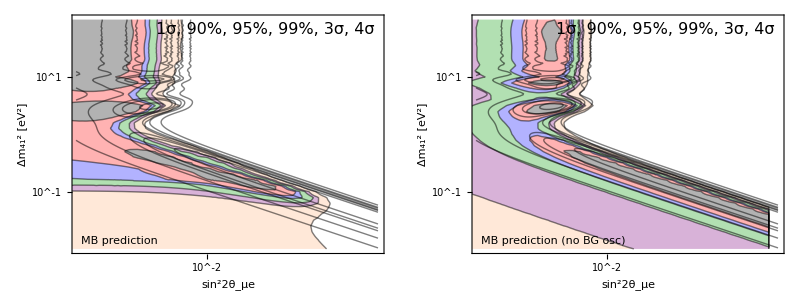

```mathematica
MyLegend=Framed[Grid[{
{LegendBox[MyFillingStyles⟦1⟧,Directive[Black,Thin]],"1σ (our fit)"},
{LegendBox[MyFillingStyles⟦2⟧,Directive[Black,Thin]],"90%"},
{LegendBox[MyFillingStyles⟦3⟧,Directive[Black,Thin]],"95%"},
{LegendBox[MyFillingStyles⟦4⟧,Directive[Black,Thin]],"99%"},
{LegendBox[MyFillingStyles⟦5⟧,Directive[Black,Thin]],"3σ%"},
{LegendBox[MyFillingStyles⟦6⟧,Directive[Black,Thin]],"4σ"},
{LegendLine[Black],"MB official"}
},Spacings->{0.3,0.2},Alignment->{{Center,Left},Automatic}],Background->GrayLevel[1,.8]];
(*MyLabels={
"only ν_μ→ν_e oscillations",
"ν_μ→ν_e oscillations\n+ signal normalization 1/P_μμ",
"ν_μ→ν_e oscillations\n+ signal normalization 1/P_μμ\n+ ν_e disappearance",
"ν_μ→ν_e oscillations\n+ signal normalization 1/P_μμ\n+ ν_e disappearance\n+ ν_μ disappearance"
};*)
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=Show[cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{{-3.5,Full},Full,Full},Contours->MyContours,ContourShading->MyFillingStyles,ContourStyle->Directive[Black,Thin],FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}}]],
MBPlot,Epilog->{(*Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],*)
Text[MyTunesHumanReadable⟦i⟧,Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,.7]],
Text[Style["1σ, 90%, 95%, 99%, 3σ, 4σ",FontSize->16],Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]]}];
];
MyPlotGrid=Grid[{{MyPlot[1],MyPlot[2]}}]
(*MyPlotGrid=Grid[{{MyPlot[1],MyPlot[2]},{MyPlot[3],MyPlot[4]},{MyPlot[5],MyPlot[6]},{MyPlot[7],MyPlot[8]}}]*)
```

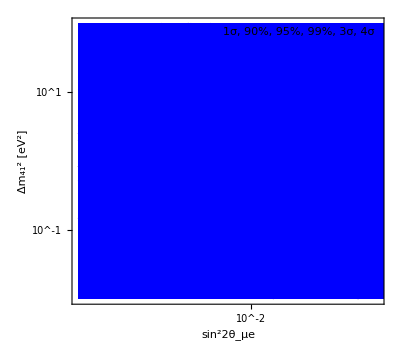

```mathematica
i=1;
MyContourPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{{-4,Full},Full,Full},Contours->MyContours,ContourShading->None,ContourStyle->(*Directive[Blue,Thick]*)(Directive[Thick,#,Opacity[1]]&/@MyFillingStyles)]];
(*MyContourPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{{-4,Full},Full,Full},Contours->MyContours,ContourShading->MyFillingStyles,ContourStyle->Directive[Black,Thin]]];*)
MyUμ4Plot[i]=DensityPlot[(DataUμ4Interpol[i][logdmsq,logth])^2,{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},ColorFunction->{RGBColor[0,0,1,Clip[1-0.5(#/0.02),{0,.5}]]&},ColorFunctionScaling->False,PlotPoints->50];
i=2;
MyContourPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{{-4,Full},Full,Full},Contours->MyContours,ContourShading->False,ContourStyle->Directive[Black,Thick,Dashed]]];

Show[MyContourPlot[1],MyContourPlot[2],(*MBPlot,*)MyUμ4Plot[1],PlotRange->{{-4,Log10[0.3]},{-2,2}},FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
Epilog->{(*Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],*)
Text["1σ, 90%, 95%, 99%, 3σ, 4σ",Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]]}]
```

```mathematica
Export["~/mb-contours.pdf",MyPlotGrid]
```

~/mb-contours.pdf

### Exclusion Regions in U_μ4^2 and Δm^2

```mathematica
MyTunes={"default","default-nobgosc","gibuu","nuance","nuwro","G18_01a_02_11a","G18_01b_02_11a","G18_02a_02_11a","G18_02b_02_11a","G18_10a_02_11a","G18_10b_02_11a"};
(*MyTunes={"default","default-nobgosc"};*)
MyTunesHumanReadable={"MB prediction (no BG osc)","MB prediction","GiBUU","NUANCE","NuWro",
"GENIE G18_01a_02_11a","GENIE G18_01b_02_11a","GENIE G18_02a_02_11a","GENIE G18_02b_02_11a","GENIE G18_10a_02_11a","GENIE G18_10b_02_11a"};
DataFiles="3-3p1/mbbg/dm41s22thmueUm4-mbjk-"<>#<>".dat"&/@MyTunes;
For[i=1,i≤Length[DataFiles],i++,
If[FileExistsQ[StringReplace[DataFiles⟦i⟧,".dat":>"-stripped.dat"]],
DataRaw[i]=KPImport[StringReplace[DataFiles⟦i⟧,".dat":>"-stripped.dat"],"Table"],
(* Else *)
DataRaw[i]=KPImport[DataFiles⟦i⟧,"Table"]
];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]=Select[Data[i],#⟦3⟧<0.75&]; (* select Subscript[U, μ4] range to avoid solutions with Subscript[U, μ4]~1 *)
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,If[10^(#⟦2⟧)/(4*(10^(#⟦3⟧))^2)>0.2,1.*^12,#⟦4⟧]}&/@Data[i]; (* restrict Subscript[U, e4] range *)
Data[i]=Gather[Sort[Data[i]],#1⟦{1,3}⟧==#2⟦{1,3}⟧&];
Data[i]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Data[i], (* save χ^2 at optimum sin^2 2 Subscript[θ, μe] *)

(* Else - data files in dm41, th14, th24 *)
Print["Wrong file format!"];
];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
Um4Min[i]=Min[Data[i]⟦All,2⟧];
Um4Max[i]=Max[Data[i]⟦All,2⟧];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

(* Extract best fit point: Either it has been computed accurately, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"s22thmue"]],Chi2Min[i]},

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
]; (* End[if] *)

Print[DataFiles⟦i⟧];
Print["   Best fit: sin^22θ_μe=",10^BFP[i]⟦2⟧,", Δm^2=",10^BFP[i]⟦1⟧];
Chi2NoOsc[i]=DataInterpol[i][logdmsqMin[i],Um4Min[i]];
Print["   χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
]; (* End[loop over data files] *)
```

3-3p1/mbbg/dm41s22thmueUm4-mbjk-default.dat

Best fit: sin^22θ_μe=1.77828, Δm^2=0.251189

χ_min^2=192.7, χ_(no osc)^2=211.77, Δχ_(no osc.)^2=19.0691 (CL 0.999928)

ReadList::strmerr: Error on stream /Users/jkopp/home-uni/papers/sterile-nu/sim/3-3p1/mbbg/dm41s22thmueUm4-mbjk-default-nobgosc.dat. Error message: Operation not permitted

3-3p1/mbbg/dm41s22thmueUm4-mbjk-default-nobgosc.dat

Best fit: sin^22θ_μe=5.30884, Δm^2=0.0398107

χ_min^2=188.602, χ_(no osc)^2=200.489, Δχ_(no osc.)^2=11.8877 (CL 0.997378)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-gibuu.dat

Best fit: sin^22θ_μe=1.20226, Δm^2=12.5893

χ_min^2=562.419, χ_(no osc)^2=674.668, Δχ_(no osc.)^2=112.249 (CL 1.)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-nuance.dat

Best fit: sin^22θ_μe=1.58489, Δm^2=0.316228

χ_min^2=197.551, χ_(no osc)^2=216.958, Δχ_(no osc.)^2=19.4072 (CL 0.999939)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-nuwro.dat

Best fit: sin^22θ_μe=1.44544, Δm^2=3.16228

χ_min^2=252.423, χ_(no osc)^2=272.627, Δχ_(no osc.)^2=20.2044 (CL 0.999959)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_01a_02_11a.dat

Best fit: sin^22θ_μe=1.31826, Δm^2=7.94328

χ_min^2=191.743, χ_(no osc)^2=205.337, Δχ_(no osc.)^2=13.5931 (CL 0.998882)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_01b_02_11a.dat

Best fit: sin^22θ_μe=1.38038, Δm^2=7.94328

χ_min^2=194.469, χ_(no osc)^2=204.795, Δχ_(no osc.)^2=10.3268 (CL 0.994278)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_02a_02_11a.dat

Best fit: sin^22θ_μe=1.25893, Δm^2=7.94328

χ_min^2=189.778, χ_(no osc)^2=201.403, Δχ_(no osc.)^2=11.6253 (CL 0.997011)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_02b_02_11a.dat

Best fit: sin^22θ_μe=1.20226, Δm^2=7.94328

χ_min^2=190.26, χ_(no osc)^2=200.348, Δχ_(no osc.)^2=10.0881 (CL 0.993552)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_10a_02_11a.dat

Best fit: sin^22θ_μe=1.31826, Δm^2=0.316228

χ_min^2=185.341, χ_(no osc)^2=196.677, Δχ_(no osc.)^2=11.3358 (CL 0.996545)

3-3p1/mbbg/dm41s22thmueUm4-mbjk-G18_10b_02_11a.dat

Best fit: sin^22θ_μe=1.25893, Δm^2=7.94328

χ_min^2=186.8, χ_(no osc)^2=199.352, Δχ_(no osc.)^2=12.5522 (CL 0.998119)

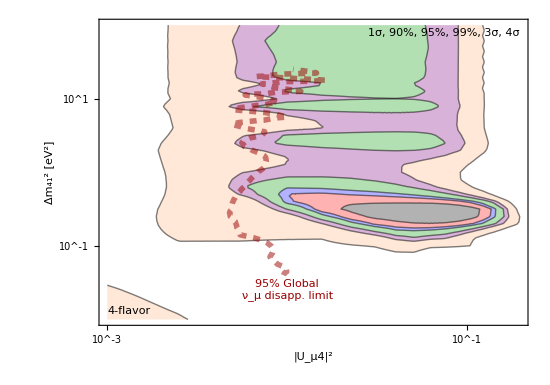
-Graphics-Brdar Kopp 2021

```mathematica
(* plots illustrating the impact of BG oscillations in MB *)
MyContours={χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyStyles={Directive[Black,Dashing[{}]],Directive[Red,Dashed],Directive[Blue,Dashing[{0.005,0.002}]],Directive[RGBColor[0,0.6,0],DotDashed],Directive[Purple,Dotted],Directive[RGBColor[1,0.7,0.5],Dashing[{}]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[1,0,0,.3],RGBColor[0,0,1,.3],RGBColor[0,0.6,0,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
For[i=1,i≤2,i++,
MyPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,Sqrt[10^logUm4sq]]-Chi2Min[i],{logUm4sq,-3,Log10[Um4Max[i]^2]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{Full,Full,Full},Contours->MyContours,
ContourShading->If[MyTunes⟦i⟧=="default",MyFillingStyles,None],
ContourStyle->If[MyTunes⟦i⟧=="default",Directive[Thin,Black],Directive[Black,Dashed]]]
];
];
DataGlobalMu=Cases[Import["3-3p1/mbbg/mona/CombinedNuMuDis.dat","Table"],{Repeated[_?NumericQ]}];
MyPlotGlobalMu=cleanContourPlot[ListContourPlot[DataGlobalMu-Min[DataGlobalMu⟦All,3⟧],PlotRange->{Full,Full,Full},Contours->{χ2[2,0.05]},
ContourShading->None,ContourStyle->Directive[RGBColor[.6,0,0],AbsoluteThickness[4],Dashed]]];
MyPlot[99]=Overlay[{JHEPPlot[Show[MyPlot[1],(*MyPlot[2],*)MyPlotGlobalMu,
FrameLabel->{"|U_μ4|^2","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
PlotRange->{{All,Log10[0.5]},All},ImagePadding->{{70,20},{60,15}},PlotRangePadding->0,ImageSize->550,AspectRatio->0.7,
Epilog->{
Text[Style["1σ, 90%, 95%, 99%, 3σ, 4σ"],Scaled[{0.98,0.97}],{1,1}(*,Background->GrayLevel[1,.7]*)],
Text["4-flavor",Scaled[{0.02,0.03}],{-1,-1},Background->GrayLevel[1,.7]],
Text[Style["95% Global\nν_μ disapp. limit",RGBColor[.6,0,0],LineSpacing->{0.9,0}],{-2,-1.45},{0,1},{1,0}]
(*Text[Style[Grid[{{"Shaded:","4-flavor"},{"Dashed:","2-flavor"}}]],Scaled[{0.02,0.03}],{-1,-1},Background->GrayLevel[1,.7]]*)
}]],Style["Brdar Kopp 2021",FontFamily->"Helvetica",FontSize->14]},Alignment->{0.9,1}]
Export["fig/mb-contours-Um4sq-default.pdf",MyPlot[99]];
```

```mathematica
MyContours={χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyStyles={Directive[Black,Dashing[{}]],Directive[Red,Dashed],Directive[Blue,Dashing[{0.005,0.002}]],Directive[RGBColor[0,0.6,0],DotDashed],Directive[Purple,Dotted],Directive[RGBColor[1,0.7,0.5],Dashing[{}]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[1,0,0,.3],RGBColor[0,0,1,.3],RGBColor[0,0.6,0,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};

For[i=1,i≤Length[DataFiles],i++,
MyContourPlot[i]=cleanContourPlot[ContourPlot[DataInterpol[i][logdmsq,Sqrt[10^logUm4sq]]-Chi2Min[i],{logUm4sq,-4,Log10[Um4Max[i]^2]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->{Full,Full,Full},Contours->MyContours,ContourShading->MyFillingStyles,ContourStyle->Directive[Black,Thin]]];
];
```

InterpolatingFunction::dmval: Input value {-1.99971,0.0100021} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

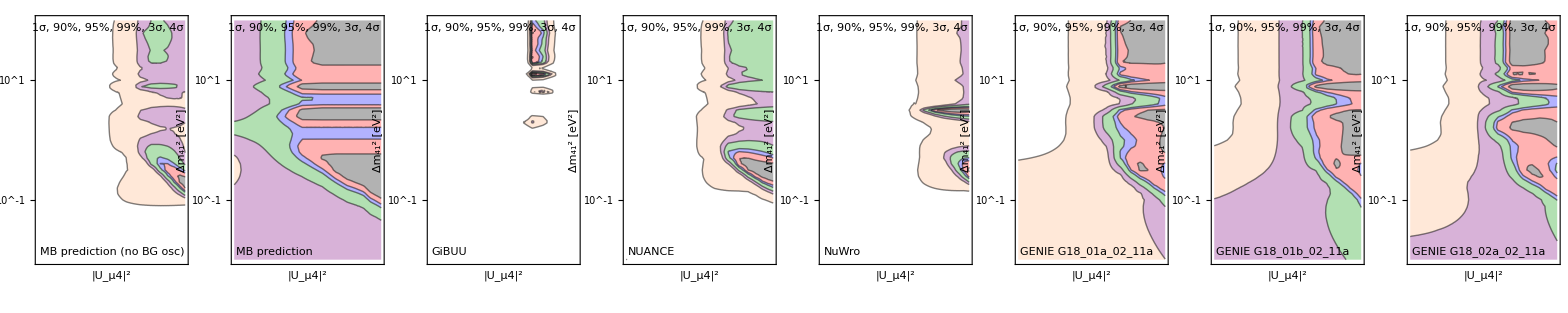

```mathematica
MyLegend=Framed[Grid[{
{LegendBox[MyFillingStyles⟦1⟧,Directive[Black,Thin]],"1σ (our fit)"},
{LegendBox[MyFillingStyles⟦2⟧,Directive[Black,Thin]],"90%"},
{LegendBox[MyFillingStyles⟦3⟧,Directive[Black,Thin]],"95%"},
{LegendBox[MyFillingStyles⟦4⟧,Directive[Black,Thin]],"99%"},
{LegendBox[MyFillingStyles⟦5⟧,Directive[Black,Thin]],"3σ%"},
{LegendBox[MyFillingStyles⟦6⟧,Directive[Black,Thin]],"4σ"},
{LegendLine[Black],"MB official"}
},Spacings->{0.3,0.2},Alignment->{{Center,Left},Automatic}],Background->GrayLevel[1,.8]];
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=Show[MyContourPlot[i],(*PlotRange->{Full,{-2,2}},*)FrameLabel->{"|U_μ4|^2","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
Epilog->{(*Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],*)
Text[MyTunesHumanReadable⟦i⟧,Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,.7]],
Text["1σ, 90%, 95%, 99%, 3σ, 4σ",Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]]}]
];
(*MyPlotGrid=Grid[{{MyPlot[1],MyPlot[2]},{MyPlot[3],MyPlot[4]},{MyPlot[5],MyPlot[6]},{MyPlot[7],MyPlot[8]}}]*)
MyPlotGrid=Grid[{{MyPlot[1],MyPlot[2],MyPlot[3],MyPlot[4],MyPlot[5],MyPlot[6],MyPlot[7],MyPlot[8]}}]
```

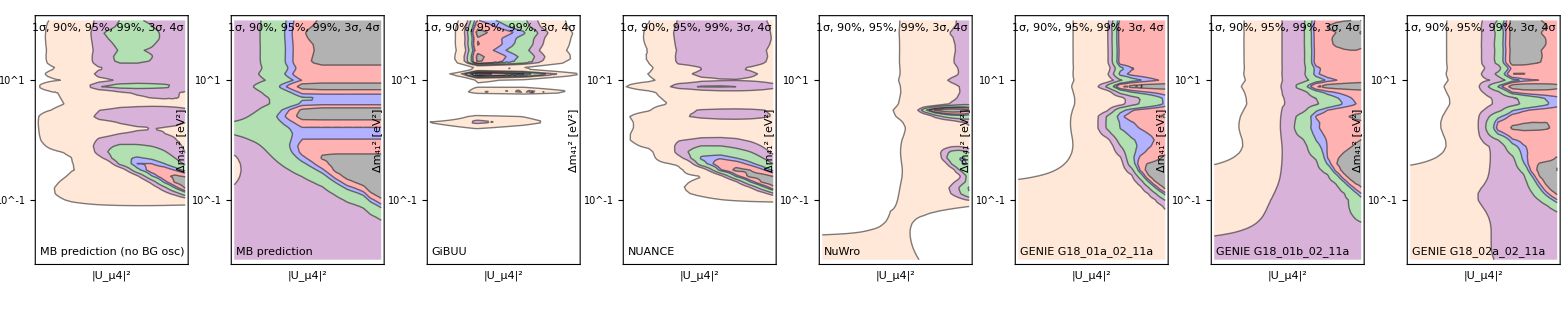

```mathematica
(* 10 sampling points for mu and e *)
```

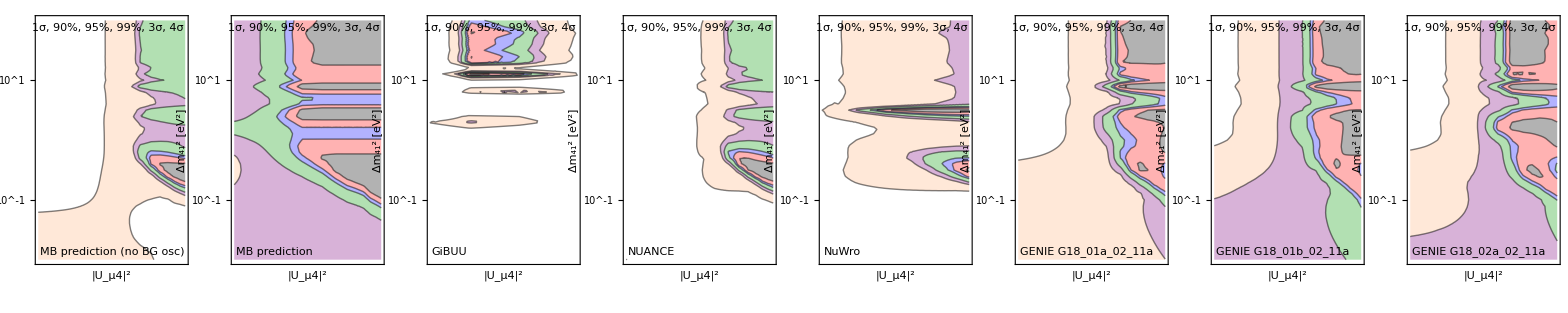

```mathematica
(* 20 sampling points for mu and e *)
```

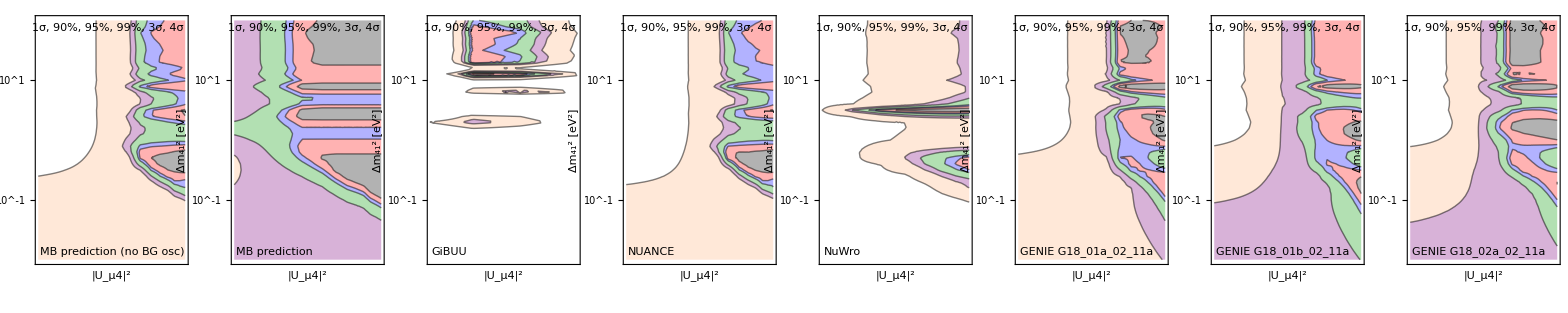

```mathematica
(* 40 sampling points for mu and e *)
```

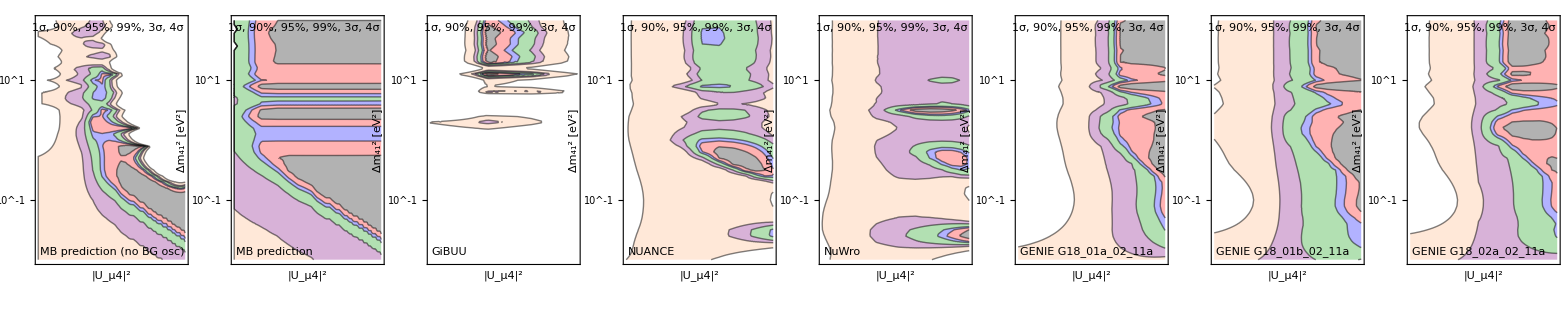

```mathematica
(* filter 0.1 *)
```

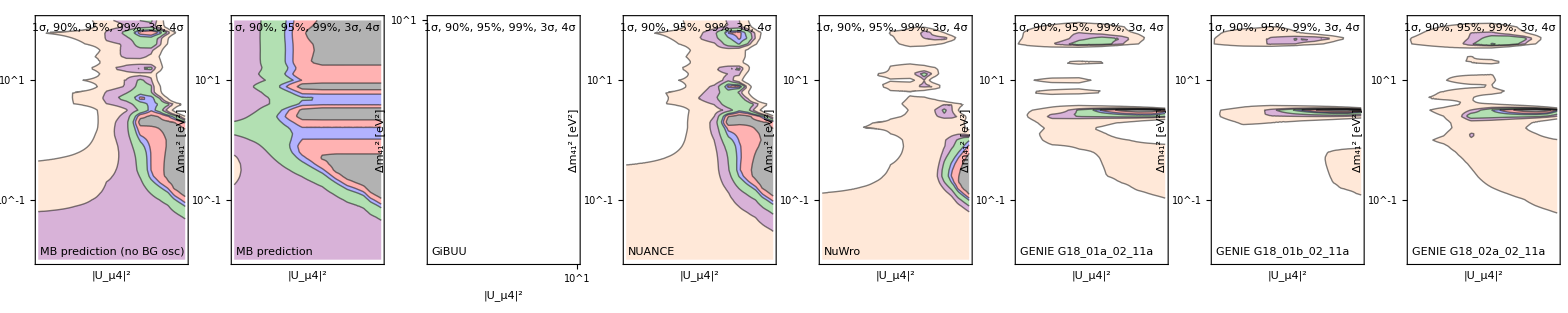

```mathematica
(* 40 sampling points for mu *)
```

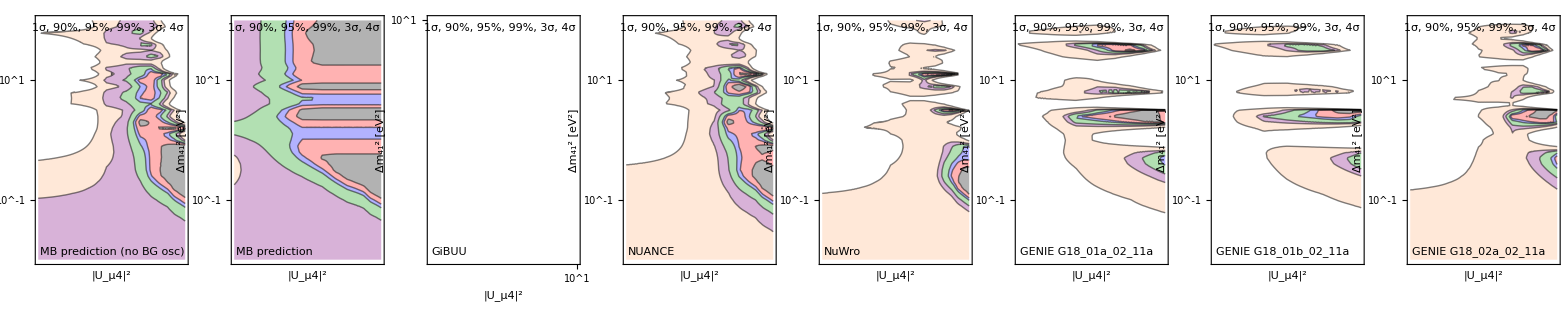

```mathematica
(* no filter *)
```

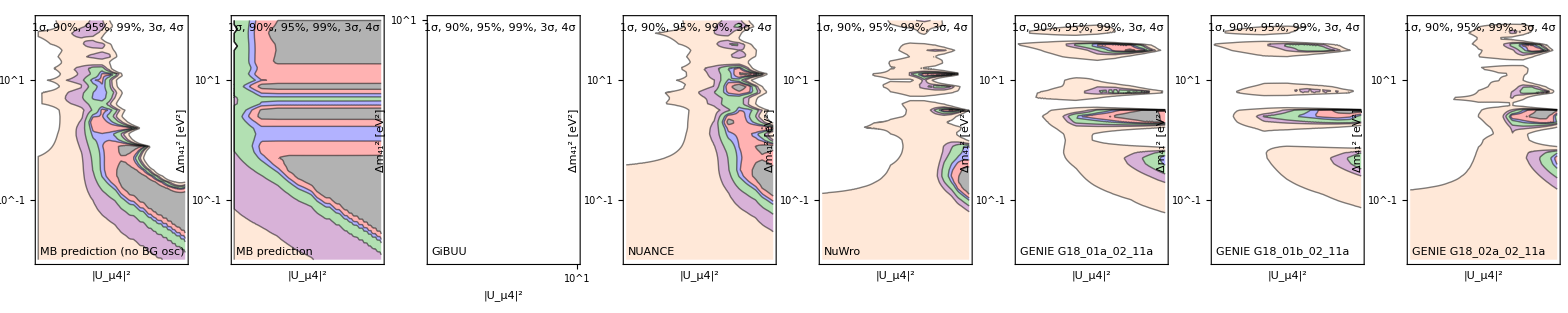

```mathematica
(* filter 0.2 *)
```

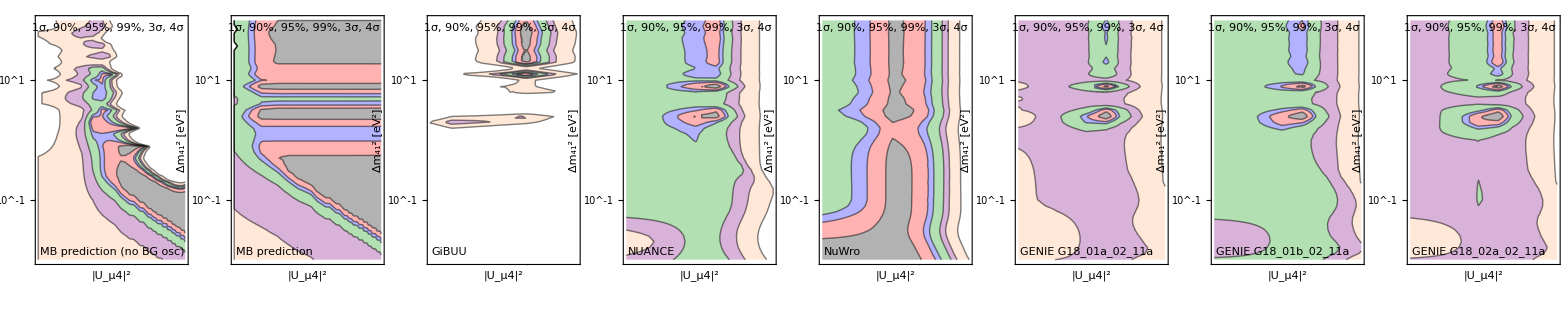

```mathematica
(* filter 0.5 *)
```

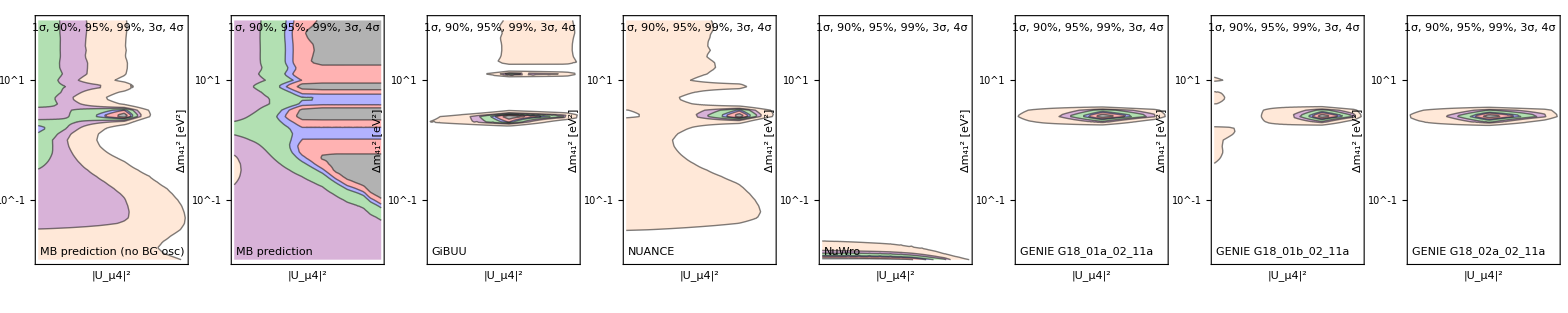

```mathematica
(* filter 0.8 *)
```